Fourier Analysis
Making a parametrized formula for my girlfriend ZSMG <3.

```mathematica
newImage=Import["C:\\Users\\user\\Desktop\\face_shapes\\zsmg_face.TIF"];
```

```mathematica
(image =
Rasterize[newImage,
ImageSize -> 1200, RasterPadding->6]) //
Show[#, ImageSize->240]&
```

-Graphics-

```mathematica
EdgeDetect[newImage] // Show[#, ImageSize->240]&
```

-Graphics-

```mathematica
edgePoints = {#2, -#1}&@@@ Position[ImageData[EdgeDetect[newImage]],1,{2}];
```

```mathematica
pointListToLines[pointList_, neighborhoodSize_:6]:= 
Module[{L = DeleteDuplicates[pointList], NF, λ,lineBag, counter, seenQ, sLB, nearest,  
            nearest1, nextPoint,couldReverseQ,  𝒹, 𝓃, 𝓈},
NF = Nearest[L] ;
     λ = Length[L];
Monitor[
(* list of segments *)
lineBag = {};
counter = 0; 
While[counter < λ,
(* new segment *)
sLB = {RandomChoice[DeleteCases[L, _?seenQ]]}; 
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ= True;
(* complete segment *)
While[(nearest = NF[Last[sLB], {Infinity, neighborhoodSize}];
           nearest1 = SortBy[DeleteCases[nearest, _?seenQ], 1.EuclideanDistance[Last[sLB],#]&];
           nearest1 =!= {} || couldReverseQ),
             If[nearest1 === {},
             (* extend the other end; penalize sharp edges *)
             sLB = Reverse[sLB]; couldReverseQ = False,
            (* prefer straight continuation *)
             nextPoint = If[Length[sLB] ≤ 3, nearest1[[1]],
                                         𝒹 = 1.Normalize[(sLB[[-1]]-sLB[[-2]]) + 1/2 (sLB[[-2]]-sLB[[-3]])];
                                         𝓃 = {-1, 1}Reverse[𝒹];
                                        𝓈 = Sort[{Sqrt[(𝒹.(# - sLB[[-1]]))^2 + 
                                                           (* perpendicular *) 2 (𝓃.(# - sLB[[-1]]))^2], # }& /@ nearest1]; 
                                        𝓈[[1,2]]];
             AppendTo[sLB, nextPoint];
            seenQ[nextPoint]=True;
           counter++ ]];
AppendTo[lineBag, sLB]];
(* return segments sorted by length *)
Reverse[SortBy[Select[lineBag , Length[#] > 12&], Length]],
(* monitor progress *)
Grid[{{Text[Style["progress point joining", Darker[Green, 0.66]]], ProgressIndicator[counter/λ]},
          {Text[Style["number of segments", Darker[Green, 0.66]]],  Length[lineBag] + 1}}, 
        Alignment -> Left, Dividers -> Center]]]
```

```mathematica
SeedRandom[22];
hLines = pointListToLines[edgePoints, 6];
Length[hLines]
```

57

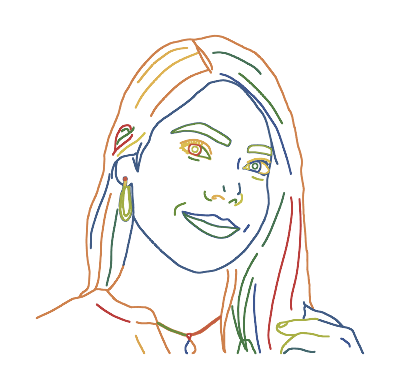

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]], Line[#]}& /@ hLines]
```

```mathematica
Graphics[BSplineCurve[#, SplineDegree -> 6, SplineClosed -> 
True]& /@ hLines]
```

-Graphics-

```mathematica
(* Fourier coefficients of a single curve *)
fourierComponentData[pointList_, nMax_, op_] := 
Module[{ε=10^-3, μ = 2^14, M = 10000,s,
             scale, Δ, L , nds, sMax, if, 𝓍𝓎Function, X, Y, XFT, YFT,type},
(* prepare curve *)
scale = 1. Mean[Table[ Max[ fl/@ pointList] - Min[fl /@ pointList],{fl,{First, Last}}]];
 Δ=EuclideanDistance[First[pointList], Last[pointList]];
 L=Which[op === "Closed", type="Closed";
                                                        If[First[pointList]===Last[pointList], 
                                                           pointList,Append[pointList, First[pointList]]], 
                op === "Open",type="Open";pointList,
                 Δ==0.,type="Closed";  pointList,
                 Δ/scale<op, type="Closed"; Append[pointList, First[pointList]],
                True,  type="Open"; Join[pointList, Rest[Reverse[pointList]]]];
(* re-parametrize curve by arclength *)
𝓍𝓎Function =BSplineFunction[L, SplineDegree->4];
nds = NDSolve[{s'[t]==Sqrt[𝓍𝓎Function'[t].𝓍𝓎Function'[t]], s[0]==0},s, 
                          {t, 0, 1}, MaxSteps -> 10^5, PrecisionGoal -> 4];
(* total curve length *)
     sMax= s[1]/.nds[[1]];
     if=Interpolation[Table[{s[σ]/.nds[[1]], σ}, {σ,0, 1, 1/M}]];
X[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[1]];
Y[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[2]]; 
(* extract Fourier coefficients *)
{XFT, YFT} = Fourier[Table[#[N @ t], {t, -Pi+ε, Pi - ε, (2Pi-2ε)/μ}]]& /@ {X, Y};   
{type,2Pi/Sqrt[μ] *
((Transpose[Table[{Re[#], Im[#]}&[Exp[I k Pi]  #[[k+1]]], {k, 0, nMax}]]& /@ {XFT, YFT}))}  ]
```

```mathematica
Options[fourierComponents] = {"MaxOrder" -> 200, "OpenClose" -> 0.025};

fourierComponents[pointLists_,OptionsPattern[]] := 
Monitor[Table[fourierComponentData[pointLists[[k]],                           
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["MaxOrder"]],
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["OpenClose"]]],
                         {k, Length[pointLists]}],
Grid[{{Text[Style["progress calculating Fourier coefficients", Darker[Green, 0.66]]], ProgressIndicator[k/Length[pointLists]]} }, 
        Alignment -> Left, Dividers -> Center]]/; Depth[pointLists] === 4
```

```mathematica
fCs = fourierComponents[hLines]; (*"OpenClose" -> Table["Closed", {Length[hLines]}]];*)
```

```mathematica
makeFourierSeries[{"Closed" | "Open", {{cax_, sax_},{cay_, say_}}}, t_, n_] :=
 {Sum[If[k==0, 1/2, 1]cax[[k+1]] Cos[k t]+sax[[k+1]] Sin[k t],{k,0, Min[n, Length[cax]]}],
 Sum[If[k==0, 1/2, 1]cay[[k+1]] Cos[k t]+say[[k+1]] Sin[k t],{k, 0,Min[n, Length[cay]]}]}
```

```mathematica
makeFourierSeriesApproximationManipulate[fCs_, maxOrder_:100] :=
Manipulate[
With[{opts = Sequence[PlotStyle -> Black, Frame -> True, Axes -> False, 
                                         FrameTicks -> None,PlotRange -> All, ImagePadding -> 12]},
Show[{
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Closed", _}]], {t, -Pi, Pi},opts],
ParametricPlot[Evaluate[ make
FourierSeries[#,t, n]& /@ Cases[fCs, {"Open", _}]], {t, -Pi, 0},opts]}] // Quiet], 
{{n, 1, "max series order"}, 1, maxOrder,1,Appearance -> "Labeled"},
TrackedSymbols :> True, SaveDefinitions -> True]
```

```mathematica
makeFourierSeriesApproximationManipulate[fCs, 100]
```

```mathematica
sinAmplitudeForm[kt_, {cF_, sF_}] := With[{φ = phase[cF, sF]}, Sqrt[cF^2+sF^2] Sin[kt+ φ]]

phase[cF_, sF_] := With[{T = Sqrt[cF^2+sF^2]},
With[{g = Total[Abs[Table[cF Cos[x] +sF Sin[x]-  T Sin[x+#1 ArcSin[cF/T]+#2],{x, 0, 1, 0.1}]]]&}, 
          If[g[1, 0]<   g[-1, Pi],  ArcSin[cF/T],Pi-ArcSin[cF/T]]]]
```

```mathematica
singleParametrization[fCs_, t_, n_] :=
 UnitStep[Sign[ Sqrt[Sin[t/2]]]] *
 Sum[UnitStep[t-((m -1)4Pi-Pi)]UnitStep[(m -1)4Pi + 3 Pi-t]*
({+fCs[[m,2, 1, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 1, 1, k+1]], fCs[[m,2, 1, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}],   
 +fCs[[m,2, 2, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 2, 1, k+1]], fCs[[m,2, 2, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}]} ),
{m, Length[fCs]}]
```

```mathematica
finalCurve = Rationalize[singleParametrization[fCs, t,100] ,10^-3];
Short[finalCurve, 13]//TraditionalForm
```

{(«1») √(sin(t/2)),(«1») √(sin(t/2))}

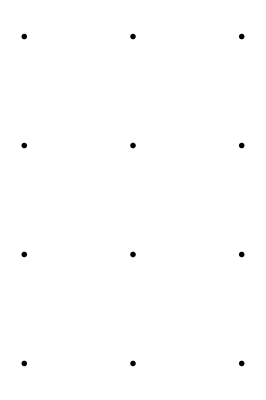

```mathematica
GraphicsGrid[Partition[With[
{opts = Sequence[ PlotStyle -> Pink, Frame -> True, Axes -> False, FrameTicks -> None,PlotRange -> All, ImagePadding -> 12 ]},
Table[Show[{
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Closed", _}]], {t, -Pi, Pi},opts],
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Open", _}]], {t, -Pi, 0},opts]},
PlotLabel -> Style[n, Bold], ImageSize -> 130, AspectRatio -> 1.00],
{n, {1, 2, 3, 4, 5, 6, 8, 10, 20,  40, 50, 100}}]],3], Spacings -> -10]
```

```mathematica
Clear[makeSegmentOrderManipulate];

makeSegmentOrderManipulate[fCs_, orderList_, maxOrder_Integer:180, graphicsOptions_Rule ...] :=
With[{nVars = Table[ToExpression["n"<>IntegerString[k]], {k, Length[fCs]}]}, 
 Manipulate[ 
Module[{ highlightColor = Directive[Thickness[0.01], Purple, Opacity[0.5]],tab,curvesNew, pos,gr},   
(* initialize variable curves *)
If[curves==={}, 
     tab=Table[ ParametricPlot[Evaluate[
{Sum[If[k==0, 1/2, 1]fCs[[m,2, 1, 1, k+1]] Cos[k t]+fCs[[m,2, 1,2, k+1]] Sin[k t],
      Evaluate[{k,0, nVars[[m]]}], Method -> "Procedural"],
Sum[If[k==0, 1/2, 1]fCs[[m,2, 2, 1, k+1]] Cos[k t]+fCs[[m,2, 2,2, k+1]] Sin[k t],
        Evaluate[{k,0, nVars[[m]]}], Method -> "Procedural"]}], 
Evaluate[{t, If[fCs[[m, 1]]==="Closed", -Pi, 0], Pi}], 
MaxRecursion -> 3,PlotRange -> All,
(* highlight segment of clicked-in slider *)
PlotStyle -> Black,  Frame -> True, Axes -> False, FrameTicks -> None, PerformanceGoal -> "Quality"],
  {m,Length[fCs]}] ; 
curves = Cases[#,_Line, ∞]& /@ tab ]; 
(* position last changed slider value *)
pos =Flatten[Position[ Abs[nVars-nVals], Except[0], {1}, Heads -> False]]; 
(* draw curve of slider moved *)
If[pos=!={},
    curvesNew=Table[Cases[
ParametricPlot[Evaluate[ With[{m = pos[[j]]}, 
{ Sum[If[k==0, 1/2, 1]fCs[[m,2, 1, 1, k+1]] Cos[k t]+fCs[[m,2, 1,2, k+1]] Sin[k t],
      Evaluate[{k,0, nVars[[m]]}], Method -> "Procedural"],
Sum[If[k==0, 1/2, 1]fCs[[m,2, 2, 1, k+1]] Cos[k t]+fCs[[m,2, 2,2, k+1]] Sin[k t],
        Evaluate[{k,0, nVars[[m]]}], Method -> "Procedural"]}]], 
Evaluate[{t, If[fCs[[m, 1]]==="Closed", -Pi, 0], Pi}], MaxRecursion -> 3,PlotRange -> All, 
Frame -> True, Axes -> False, FrameTicks -> None, PerformanceGoal -> "Quality"],_Line, ∞],
{j, Length[pos]}]; 
(* highlight changed curve *)
Do[curves = MapAt[ curvesNew[[j]]&, curves, pos[[j]]],{j, Length[pos]}]]; 
gr=Graphics[{Black, MapAt[{highlightColor,#}&,If[cN===0,curves ,  MapAt[{highlightColor,#}&, curves, cN]], 
                                     If[ControlActive[True, False], List /@ pos,{}]]}, ImageSize -> 360,graphicsOptions];
nVals=nVars; gr ]//Quiet,
(* make sliders for given segment-depending orders *)
Evaluate[ (Grid[#, Spacings -> 4]&@ 
Transpose[Join[#,Table["",{10-Length[#]}]]& /@ 
Partition[
(Control /@  MapIndexed[Function[{b, p}, MapAt[Style[p[[1]], Gray]&, b,{1, 3}]],{{#1,#2,""}, 
1, maxOrder, 1, Appearance -> "Labeled", ImageSize -> Small}&@@@
Transpose[{nVars, orderList }]]), 10,10,1,{}]])] ,
Delimiter,
{{cN, 0, "highlight\nsegment"}, 0, Length[nVars], 1,ImageSize -> Small,Appearance -> "Labeled"},
{{nVals, orderList},ControlType -> None},
{{curves, {}},ControlType -> None},
ControlPlacement -> Bottom, TrackedSymbols :> True,
SynchronousInitialization-> False, SaveDefinitions -> True]]
```

```mathematica
makeSegmentOrderManipulate[fCs, OrderList=
Last/@ {{1,100},{2,150},{3,100},{4,100},{5,100},{6,100},{7,100},{8,100},{9,100},{10,100},{11,100},{12,100},{13,100},{14,100},{15,100},{16,100},{17,100},{18,100},{19,100},{20,100},{21,100},{22,100},{23,100},{24,100},{25,100},{26,100},{27,100},{28,100},{29,100},{30,100},{31,100},{32,100},{33,100},{34,100},{35,100},{36,100},{37,100},{38,100},{39,100},{40,100},{41,100},{42,100},{43,100},{44,100},{45,100},{46,100},{47,100},{48,100},{49,100},{50,100},{51,100},{52,100},{53,100},{54,100},{55,100},{56,100},{57,100}}, 120]
```

```mathematica
zCurve = Rationalize[singleParametrization[fCs, t, OrderList] ,0.002];
(*Style[zCurve, 6]//TraditionalForm*)
```

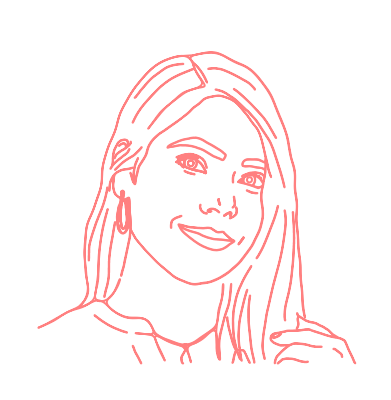

```mathematica
pp=ParametricPlot[Evaluate[N[zCurve]], {t, 0, 12 25Pi}, PlotPoints -> 2400, PlotStyle->{Thickness[0.0035],Pink}, Axes->False];
pp
```

```mathematica
Export["C:\\Users\\user\\Desktop\\face_shapes\\zsmg_black_nax_35.tiff",pp,ImageResolution->600];
```

```mathematica
finalCurve = Rationalize[singleParametrization[fCs, t,OrderList] ,0.002];
zeq=TraditionalForm[Short[finalCurve, 35]]
```

{((-1/69 sin(3/2-98 t)-1/40 sin(33/23-94 t)-1/40 sin(53/35-92 t)-1/84 sin(43/28-91 t)-1/115 sin(36/25-87 t)-1/19 sin(49/33-85 t)-1/69 sin(10/7-79 t)-1/14 sin(32/21-77 t)-1/33 sin(35/24-74 t)-1/414 sin(13/12-70 t)-1/56 sin(29/20-68 t)-1/183 sin(23/15-65 t)-1/46 sin(16/11-62 t)-1/22 sin(37/24-60 t)-1/87 sin(53/38-59 t)-1/19 sin(17/11-58 t)-1/17 sin(23/15-54 t)-1/16 sin(32/21-53 t)-1/13 sin(26/17-52 t)-1/32 sin(23/15-51 t)-1/99 sin(17/15-47 t)-1/13 sin(25/16-45 t)-1/51 sin(46/31-44 t)-1/55 sin(10/7-43 t)-1/35 sin(26/17-41 t)-1/24 sin(3/2-38 t)-1/27 sin(29/20-34 t)-2/19 sin(17/11-32 t)-1/122 sin(23/15-25 t)-1/43 sin(25/16-20 t)-29/23 sin(39/25-8 t)-774/41 sin(11/7-2 t)+114/5 sin(t+179/38)+575/41 sin(3 t+11/7)+4/19 sin(4 t+95/63)+27/14 sin(5 t+19/12)+1/31 sin(6 t+59/37)+16/11 sin(7 t+30/19)+50/49 sin(9 t+30/19)+7/13 sin(10 t+19/12)+21/64 sin(11 t+11/7)+7/24 sin(12 t+8/5)+17/27 sin(13 t+52/33)+5/24 sin(14 t+43/27)+8/17 sin(15 t+30/19)+2/21 sin(16 t+31/19)+10/33 sin(17 t+52/33)+4/25 sin(18 t+113/24)+4/23 sin(19 t+30/19)+3/11 sin(21 t+19/12)+2/23 sin(22 t+29/18)+1/12 sin(23 t+11/7)+1/18 sin(24 t+29/18)+2/29 sin(26 t+127/27)+1/44 sin(27 t+25/17)+1/20 sin(28 t+113/24)+4/23 sin(29 t+63/40)+1/59 sin(30 t+73/16)+1/12 sin(31 t+21/13)+5/26 sin(33 t+51/32)+1/17 sin(35 t+61/13)+2/27 sin(36 t+8/5)+2/27 sin(37 t+29/18)+1/22 sin(39 t+27/17)+1/24 sin(40 t+78/47)+3/29 sin(42 t+37/23)+1/193 sin(46 t+117/28)+1/104 sin(48 t+18/11)+1/90 sin(49 t+17/11)+1/57 sin(50 t+75/16)+1/36 sin(55 t+23/15)+1/68 sin(56 t+205/44)+1/64 sin(57 t+25/16)+1/54 sin(61 t+61/13)+1/53 sin(63 t+30/19)+1/62 sin(64 t+25/16)+1/86 sin(66 t+43/23)+1/227 sin(67 t+26/15)+1/34 sin(69 t+27/17)+1/155 sin(71 t+124/27)+1/40 sin(72 t+108/23)+1/13 sin(73 t+34/21)+1/20 sin(75 t+28/17)+1/267 sin(76 t+25/13)+1/19 sin(78 t+19/12)+1/42 sin(80 t+61/13)+1/75 sin(81 t+22/13)+1/48 sin(82 t+28/17)+1/35 sin(83 t+48/31)+1/30 sin(84 t+47/10)+1/33 sin(86 t+29/18)+1/62 sin(88 t+80/17)+1/450 sin(89 t+51/25)+1/36 sin(90 t+30/19)+1/67 sin(93 t+22/13)+1/144 sin(95 t+31/19)+1/219 sin(96 t+47/10)+1/68 sin(97 t+22/13)+1/77 sin(99 t+8/5)+1/476 sin(100 t+33/20)+49835/23) 227 π-t t-223 π+«55»+(-86/15 sin(87/65-85 t)-33/7 sin(4/7-83 t)-19/9 sin(1/2-78 t)-112/33 sin(27/34-72 t)-60/19 sin(16/17-71 t)-142/19 sin(81/82-65 t)-2/21 sin(12/17-61 t)-247/37 sin(17/11-36 t)-1153/37 sin(16/13-29 t)-185/8 sin(3/16-21 t)-635/23 sin(12/25-19 t)-1161/14 sin(23/26-18 t)-2279/23 sin(35/69-15 t)-4092/23 sin(41/31-6 t)-748/5 sin(3/8-4 t)-14897/19 sin(19/22-3 t)+131/56 sin(96 t)+20907/17 sin(t+56/23)+6248/3 sin(2 t+65/23)+1403/19 sin(5 t+71/23)+5989/22 sin(7 t+59/14)+1072/21 sin(8 t+22/5)+2936/19 sin(9 t+9/7)+2768/19 sin(10 t+111/28)+3388/31 sin(11 t+23/26)+2285/31 sin(12 t+53/44)+748/9 sin(13 t+10/49)+4961/36 sin(14 t+17/18)+2386/31 sin(16 t+1/33)+803/31 sin(17 t+3/19)+2215/54 sin(20 t+67/17)+80/9 sin(22 t+14/5)+677/18 sin(23 t+45/13)+858/49 sin(24 t+35/24)+295/16 sin(25 t+107/54)+312/23 sin(26 t+89/23)+662/25 sin(27 t+69/34)+525/17 sin(28 t+11/7)+977/31 sin(30 t+59/32)+888/35 sin(31 t+7/2)+588/19 sin(32 t+27/31)+913/31 sin(33 t+67/20)+560/19 sin(34 t+6/7)+581/58 sin(35 t+99/29)+797/21 sin(37 t+53/21)+53/3 sin(38 t+2/3)+289/25 sin(39 t+60/19)+41/6 sin(40 t+74/27)+678/31 sin(41 t+40/17)+85/22 sin(42 t+1/5)+119/11 sin(43 t+58/27)+227/16 sin(44 t+47/18)+115/27 sin(45 t+35/18)+556/47 sin(46 t+20/7)+367/29 sin(47 t+45/16)+139/9 sin(48 t+128/77)+187/25 sin(49 t+213/58)+241/23 sin(50 t+61/34)+2172/167 sin(51 t+94/31)+140/13 sin(52 t+47/31)+64/5 sin(53 t+109/54)+108/23 sin(54 t+5/23)+62/23 sin(55 t+9/10)+46/19 sin(56 t+90/37)+58/9 sin(57 t+18/23)+19/23 sin(58 t+185/92)+72/13 sin(59 t+4/27)+127/29 sin(60 t+50/11)+191/31 sin(62 t+23/8)+157/22 sin(63 t+3/23)+149/23 sin(64 t+26/9)+317/44 sin(66 t+37/15)+59/29 sin(67 t+94/23)+185/33 sin(68 t+21/25)+139/28 sin(69 t+58/13)+71/21 sin(70 t+1/18)+45/29 sin(73 t+11/5)+79/18 sin(74 t+2/21)+53/10 sin(75 t+77/17)+80/29 sin(76 t+13/3)+103/26 sin(77 t+35/18)+23/31 sin(79 t+7/10)+71/20 sin(80 t+82/19)+41/13 sin(81 t+2/25)+11/7 sin(82 t+36/11)+27/22 sin(84 t+23/11)+37/19 sin(86 t+491/164)+17/20 sin(87 t+49/25)+sin(88 t+7/5)+53/32 sin(89 t+55/16)+15/8 sin(90 t+41/13)+30/19 sin(91 t+53/15)+21/13 sin(92 t+51/20)+39/11 sin(93 t+29/36)+29/12 sin(94 t+5/14)+128/57 sin(95 t+16/11)+12/17 sin(97 t+24/29)+57/26 sin(98 t+54/13)+11/3 sin(99 t+19/33)+73/23 sin(100 t+47/11)+180632/51) 3 π-t t+π) √(sin(t/2)),((«107»+1/(«2») «1»+1/53 sin(75 t+21/13)+1/24 sin(76 t+8/5)+1/137 sin(78 t+49/26)+1/45 sin(80 t+34/23)+1/11 sin(81 t+47/29)+1/66 sin(83 t+17/10)+1/86 sin(84 t+29/20)+1/45 sin(85 t+29/18)+1/122 sin(87 t+38/21)+1/30 sin(88 t+27/17)+1/99 sin(89 t+79/53)+1/98 sin(90 t+32/7)+1/269 sin(91 t+15/11)+1/171 sin(92 t+13/7)+1/128 sin(95 t+47/31)+1/269 sin(96 t+151/33)+1/89 sin(98 t+77/46)+1/455 sin(99 t+72/41)-112693/29) 227 π-t t-223 π+(«113»+1/22 sin(98 t+26/17)+1/99 sin(99 t+22/43)+1/42 sin(100 t+35/24)-203236/51) 223 π-t t-219 π+(«1») 219 π-t t-215 π+«52»+(«1») 7 π-t t-3 π+(«125»+53/23 sin(91 t+19/32)+18/13 sin(92 t+53/38)+23/21 sin(93 t+76/17)+8/5 sin(94 t+13/17)+25/23 sin(95 t+93/20)+14/15 sin(98 t+57/13)+49/15 sin(99 t+17/18)+69/28 sin(100 t+86/19)-101531/22) 3 π-t t+π) √(sin(t/2))}

```mathematica
eqImg=Rasterize[zeq,ImageSize->300, ImageResolution->400]
```

-Graphics-

```mathematica
Export["C:\\Users\\user\\Desktop\\face_shapes\\zsmg_eq.tiff",eqImg,ImageResolution->400];
```